# Bottle-Flip System Identification by Kalman Filtering Brian Beckman February 2024

## Introduction

The purpose of this exercise is to measure constant physical parameters of the “bottle-flip” trick, modeled as a damped spring-mass system. We measure the parameters from observations of its spin angle and (optionally) displacement. The estimated parameters are mass, spring constant, damping constant, and resting (zero-energy) length of the system. The activity of measuring physical constants from observations is sometimes called system identification.

In the famous “bottle-flip” trick, a partially filled bottle of water is spun by human hands and settles on a surface right-side up without “kicking out.” The trick works because the water sloshes out to both ends of the bottle under centrifugal force, increasing the polar moment of inertia and decreasing the spin rate via conservation of angular momentum. The initial spin rate is much larger than the final spin rate. The final spin rate is slow enough that friction with the landing surface can keep the bottle from sliding out or tipping over. The physics is comparable to the famous demonstration whereby an ice skater slows or speeds up spin rate by extending or retracting the arms, dynamically changing polar moment of inertia.

This work is interesting for several reasons:

The bottle-flip trick is initially puzzling.

A simple, classical model without fluid dynamics suffices to explain a lot of it.

The system can be identified via a standard Extended Kalman Filter.

The elegant software-engineering technique of foldable functions pertains.

This notebook assumes proficiency with Lagrangian and Hamiltonian mechanics, Extended Kalman Filtering, and Runge-Kutta integration.

### Preliminaries

```mathematica
Needs["NumericalCalculus`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
ClearAll[toSI];
toSI[magn_,unit_]:=QuantityMagnitude[UnitConvert[Quantity[magn,unit]]];
```

## Springy, Damped, Spinning Dumbbell

The system is illustrated in the following figure, wherein m is the mass distributed in two weights at the end of a spring with spring constant k, resting (zero-energy) length l, and damping constant ν (Greek “nu”). These are parameters we’re going to measure by observing the system “in-flight.” The kinetic energy 𝒯, potential energy 𝒱, Lagrangian ℒ, state-space form Ψ, and the Euler-Lagrange equations for dynamics are written in longhand in the figure.

-Graphics-

### Setup

The 2D problem has two degrees .7f.7fof freedom: extension q of the spring and angle θ with respect to the horizontal axis of the inertial (free-fall) frame. Let q be the distance between two equal masses m/2. Let the origin of frame be the center of the bar. Each mass moves with speed q'[τ]/2 with respect to that origin.

The kinetic energy as a function of time τ is

```mathematica
T=1/2( m/2((-q'[τ])/2)^2+ m/2(q'[τ]/2)^2)+1/2(m/2((-q[τ])/2)^2+m/2(q[τ]/2)^2)θ'[τ]^2
```

1/8 m q'[τ]^2+1/8 m q[τ]^2 θ'[τ]^2

The conjugate momenta are

```mathematica
{pq[τ],pθ[τ]}==(D[T,#]&/@{q'[τ],θ'[τ]})
```

{pq[τ],pθ[τ]}=={1/4 m q'[τ],1/4 m q[τ]^2 θ'[τ]}

The Lagrangian velocities, in terms of the Hamiltonian variables, are:

```mathematica
hams=Solve[%,{q'[τ],θ'[τ]}]
```

{{q'[τ]→(4 pq[τ])/m,θ'[τ]→(4 pθ[τ])/(m q[τ]^2)}}

Therefore, the kinetic energy, in Hamiltonian terms, is

```mathematica
T/.First[hams]
```

(2 pq[τ]^2)/m+(2 pθ[τ]^2)/(m q[τ]^2)

The potential energy, for both the Lagrangian and the Hamiltonian, with the resting length, l, a constant, is

```mathematica
V=1/2 k(q[τ]-l)^2
```

1/2 k (-l+q[τ])^2

The dissipative force on each mass is half the total, so the total, for the Lagrangian, is

```mathematica
f=-ν q'[τ]
```

-ν q'[τ]

For the Hamiltonian, it is

```mathematica
f/.First[hams]
```

-(4 ν pq[τ])/m

The Lagrangian equations of motion follow here. Note that they are computed symbolically, for reliability, via Wolfram’s derivative operator, D (it’s too easy to make a mistake by hand, even with a tiny system like this one).

```mathematica
With[{Lcrds={q[τ],θ[τ]}},
With[{Lvels=D[Lcrds,τ],L=T-V},
With[{Lncnf={-ν ,0}*Lvels},
Leqns=Flatten@MapThread[
{q,v,h}↦D[D[L,v],τ]-D[L,q]==h,
{Lcrds,Lvels,Lncnf}]//FullSimplify]]]
```

{4 k l+m q[τ] θ'[τ]^2==4 k q[τ]+4 ν q'[τ]+m q''[τ],m q[τ] (2 q'[τ] θ'[τ]+q[τ] θ''[τ])==0}

The Hamiltonian equations of motion are more compact and devoid of puns between the second argument q̇ of ℒ and the time derivatives of generalized coordinates:

```mathematica
With[{Hcrds={q[τ],θ[τ]},
Hmoms={pq[τ],pθ[τ]},
H=(T+V)/.First[hams]},
With[{Hncnf={-(4ν)/m,0}*Hmoms},
Flatten@MapThread[{q,p,f}↦{D[H,q]==f-D[p,τ],D[H,p]==D[q,τ]},{Hcrds,Hmoms,Hncnf}]//FullSimplify]]
```

{(4 ν pq[τ])/m+k q[τ]+pq'[τ]==k l+(4 pθ[τ]^2)/(m q[τ]^3),q'[τ]==(4 pq[τ])/m,pθ'[τ]==0,(4 pθ[τ])/(m q[τ]^2)==θ'[τ]}

### State-Space Form

The forms above are suitable for numerical integration of ground truth via built-in integrators (last section of the notebook). We need symbolic forms for derivations below.

#### State Vector

```mathematica
Ψ=({{q}, {qdot}, {θ}, {θdot}, {m}, {k}, {ν}, {l}});
```

#### Exact System Dynamics

We employ exact dynamics to generate fake observations as well as for ground truth.

Lagrangian equations of motion in state-space form:

```mathematica
Solve[Leqns,{q''[τ],θ''[τ]}]//FullSimplify
```

{{q''[τ]→(4 k l-4 k q[τ]-4 ν q'[τ]+m q[τ] θ'[τ]^2)/m,θ''[τ]→-(2 q'[τ] θ'[τ])/q[τ]}}

These equations are non-linear in the components of the state vector. Write them in affine form for subsequent linearization in the Extended Kalman Filter (EKF):

```mathematica
ClearAll[symRules];
symRules[ψ_,x_]:=Flatten@Quiet@({{ψ⟦1,1⟧->x⟦1,1⟧}, {ψ⟦2,1⟧->x⟦2,1⟧}, {ψ⟦3,1⟧->x⟦3,1⟧}, {ψ⟦4,1⟧->x⟦4,1⟧}, {ψ⟦5,1⟧->x⟦5,1⟧}, {ψ⟦6,1⟧->x⟦6,1⟧}, {ψ⟦7,1⟧->x⟦7,1⟧}, {ψ⟦8,1⟧->x⟦8,1⟧}});
```

```mathematica
ClearAll[Dx];
Dx[x_,t_]:=(({{0, 1, 0, 0, 0, 0, 0, 0}, {-(4 k)/m, -(4 ν)/m, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}).Ψ+({{0}, {(4k l)/m+q θdot^2}, {0}, {-(2qdot  θdot)/q}, {0}, {0}, {0}, {0}}))//.symRules[Ψ,x];
Dx[Ψ,τ]//MatrixForm
```

(qdot
(4 k l)/m-(4 k q)/m+q θdot^2-(4 qdot ν)/m
θdot
-(2 qdot θdot)/q
0
0
0
0)

TODO: worry about dividing by q when it’s exactly zero.

#### Initial Conditions

Pick initial conditions to achieve a pleasing and plausible integration for the bottle-flip problem. Start with an initial separation of 1 inch (water just beginning to slosh out), 0 for initial velocity and initial angle, and 1440 angular degrees per second. Begin with Bayesian priors for the Kalman filter of 10 ounces for the mass m, 0.0057 lbf/inch for the spring constant, 0.003 lbf-sec/inch for the damping constant, and 1 inch for the resting length. The values of these last four parameters will be updated and refined by accumulating observations of separation q and angle θ.

```mathematica
(x0=({{q0=toSI[1,"inch"]}, {qdot0=0}, {θ0=0}, {θdot0=toSI[1440,"angular degree/sec"]}, {m0=toSI[10,"ounce"]}, {k0=toSI[0.0057101471547,"lbf/inch"]}, {ν0=toSI[0.003,"lbf*sec/inch"]}, {l0=toSI[1,"inch"]}})//N)//MatrixForm
```

(0.0254
0.
0.
25.1327
0.283495
1.
0.525381
0.0254)

#### Integration

The following integrator can handle dynamics that depend explicitly on time, even though dynamics in this application do not depend explicitly on time.7f.7f.

TODO: partially evaluate or lambda lift over Dx (exact non-linear dynamics). No reason to keep passing that in.

```mathematica
rk4Accumulator[{tIgnore_,x_},{dt_,t_,Dx_}]:=
With[{dx1=dt Dx[x,t]},
With[{dx2=dt Dx[x+.5 dx1,t+0.5dt]},
With[{dx3=dt Dx[x+.5 dx2,t+0.5dt]},
With[{dx4=dt Dx[x+dx3,t+dt]},
{t+dt,x+(dx1+2. dx2+2. dx3+dx4)/6.}]]]]
```

#### Verification

Reproduce ground-truth extracted ex-post-facto from the bottom “ground-truth” section of the notebook. This is not exactly cheating. Instead, it amounts to iteration-to-convergence of the entire exercise.

```mathematica
stepsPerSec=25.;h=1/stepsPerSec;
```

The integrator is foldable, with all the pursuant advantages (see [KF1]). Promote Wolfram’s Part, denoted by doubled square brackets, to a pattern-function that returns a function that can be invoked in the body of the integrator.

```mathematica
ClearAll[part];
part[ns___]:=#⟦ns⟧&;
```

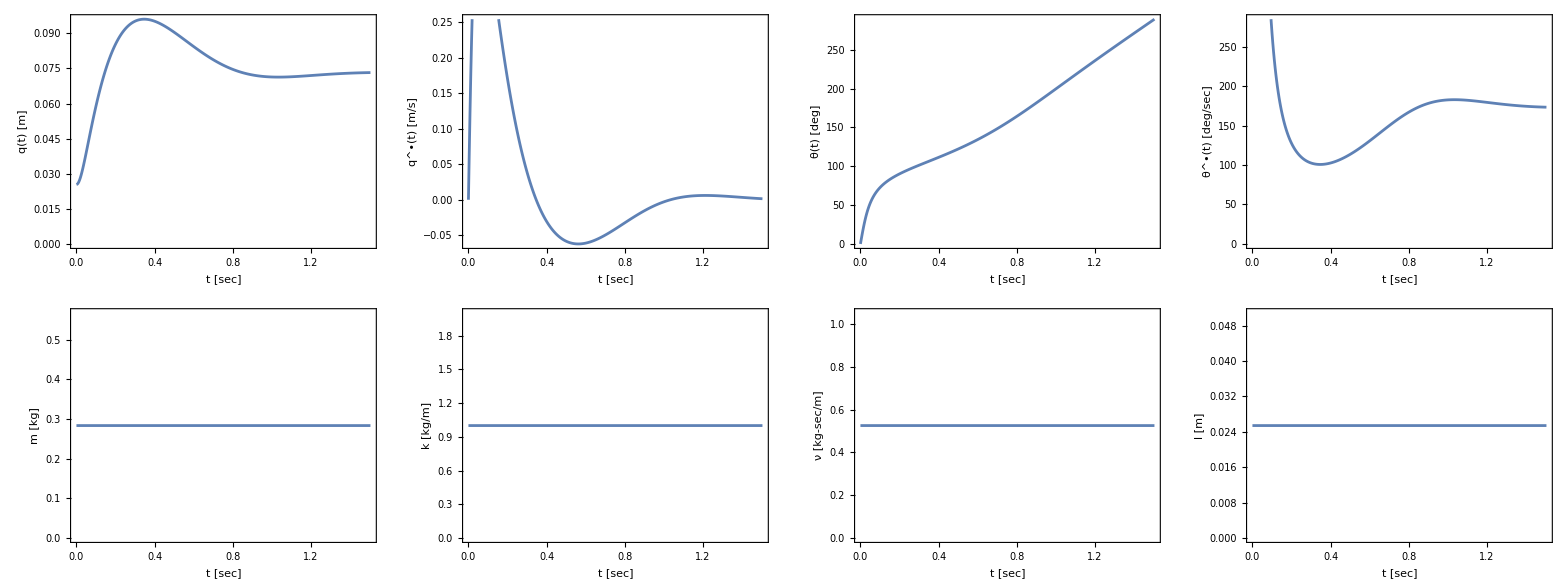

```mathematica
integration=With[{dt=h/10.0},FoldList[rk4Accumulator,{0.,x0},Table[{dt,t,Dx},{t,0.0,1.5,dt}]]];
ClearAll[plotIntegration];
plotIntegration[times_,integration_]:=
With[{intPart=n↦part[n,1]/@integration,tymlbl={"t [sec]",""}},
Grid[{
{ListLinePlot[{{times,intPart[1]}ᵀ},Frame->True,FrameLabel->{{"q(t) [m]",""},tymlbl}],
ListLinePlot[{{times,intPart[2]}ᵀ},Frame->True,FrameLabel->{{"q^•(t) [m/s]",""},tymlbl}],
ListLinePlot[{{times,intPart[3]/°}ᵀ},Frame->True,FrameLabel->{{"θ(t) [deg]",""},tymlbl}],
ListLinePlot[{{times,intPart[4]/°}ᵀ},Frame->True,FrameLabel->{{"θ^•(t) [deg/sec]",""},tymlbl}]},
{ListLinePlot[{{times,intPart[5]}ᵀ},Frame->True,FrameLabel->{{"m [kg]",""},tymlbl}],
ListLinePlot[{{times,intPart[6]}ᵀ},Frame->True,FrameLabel->{{"k [kg/m]",""},tymlbl}],
ListLinePlot[{{times,intPart[7]}ᵀ},Frame->True,FrameLabel->{{"ν [kg-sec/m]",""},tymlbl}],
ListLinePlot[{{times,intPart[8]}ᵀ},Frame->True,FrameLabel->{{"l [m]",""},tymlbl}]}
}]   ];
plotIntegration[part[1]/@integration,part[2]/@integration]
```

### Prediction (System Dynamics)

This section assumes proficiency with the Extended Kalman Filter. See Zarchan and Musoff or Bruce Gibbs for background.

#### The Fundamental Matrix

The exact, nonlinear dynamics have the form

x^•=Dx[x,t]

As dt→0, the following recurrence follows from the definition of the time derivative (overdot). With a non-infinitesimal dt, this is the first-order Taylor approximation for a state-update recurrence, also known as forward-Euler integration.

x←x+Dx[x,t]dt

For the discrete problem, we seek a fundamental Matrix F[x,t] with the state vector x factored out of Dx as follows:

x^•=F[x,t] • x

Dx[x,t]=F[x,t]• x

Start with the Jacobian of the exact dynamics:

∂_x x^•=∂Dx[x,t]/∂x

Sanity-check the integration with the following, first-order recurrence:

x←x+F[x,t] • x dt + Ω(dt^2)

The exact form differs from the Jacobian by.7f 2q (θ^•)^2. Also notice that terms in the fourth row diverge when q(t)==0 (TODO: deal with that).

```mathematica
ClearAll[F];
Module[{tt},
Module[{J=Table[D[Dx[Ψ,tt]⟦i,1⟧,Ψ⟦j,1⟧],{i,8},{j,8}]},
F[x_,t_]:=
J//.symRules[Ψ,x]//.{tt->t}]];
F[Ψ,τ]//FullSimplify//MatrixForm
(F[Ψ,τ].Ψ-Dx[Ψ,τ]//FullSimplify//MatrixForm)
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-(4 k)/m+θdot^2 | -(4 ν)/m | 0 | 2 q θdot | (4 k (-l+q)+4 qdot ν)/m^2 | (4 (l-q))/m | -(4 qdot)/m | (4 k)/m
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
(2 qdot θdot)/q^2 | -(2 θdot)/q | 0 | -(2 qdot)/q | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0
2 q θdot^2
0
0
0
0
0
0)

“Regularize” the fundamental matrix by hacking out the offending term:

```mathematica
ClearAll[F];
Module[{tt},
Module[{J=Table[D[Dx[Ψ,tt]⟦i,1⟧,Ψ⟦j,1⟧],{i,8},{j,8}]},
J⟦2,4⟧=0;(* HACK HACK HACK HACK HACK HACK HACK HACK *)
F[x_,t_]:=
J//.symRules[Ψ,x]//.{tt->t}]];
F[Ψ,τ]//FullSimplify//MatrixForm
(*(F[Ψ,τ].Ψ//FullSimplify//MatrixForm)*)
(*(Dx[Ψ,τ]//FullSimplify//MatrixForm)*)
(F[Ψ,τ].Ψ-Dx[Ψ,τ]//FullSimplify//MatrixForm)
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-(4 k)/m+θdot^2 | -(4 ν)/m | 0 | 0 | (4 k (-l+q)+4 qdot ν)/m^2 | (4 (l-q))/m | -(4 qdot)/m | (4 k)/m
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
(2 qdot θdot)/q^2 | -(2 θdot)/q | 0 | -(2 qdot)/q | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0
0
0
0
0
0
0
0)

Investigate equation 6 numerically. Make a foldable anonymous function inline, with multiples of h playing the role of a finite dt.

The following is just plotting code. No interesting dynamics here.

```mathematica
ClearAll[plotIntegrations];
plotIntegrations[tRef_,iRef_,times_,intgs_]:=
With[{ip={n,ys}↦part[n,1]/@ys,tymlbl={"t [sec]",""}},
Grid[{
{ListLinePlot[{{tRef,ip[1,iRef]}ᵀ,{times,ip[1,intgs]}ᵀ},Frame->True,FrameLabel->{{"q(t) [m]",""},tymlbl}],
ListLinePlot[{{tRef,ip[2,iRef]}ᵀ,{times,ip[2,intgs]}ᵀ},Frame->True,FrameLabel->{{"q^•(t) [m/s]",""},tymlbl}],
ListLinePlot[{{tRef,ip[3,iRef]/°}ᵀ,{times,ip[3,intgs]/°}ᵀ},Frame->True,FrameLabel->{{"θ(t) [deg]",""},tymlbl}],
ListLinePlot[{{tRef,ip[4,iRef]/°}ᵀ,{times,ip[4,intgs]/°}ᵀ},Frame->True,FrameLabel->{{"θ^•(t) [deg/sec]",""},tymlbl}]},
{ListLinePlot[{{tRef,ip[5,iRef]}ᵀ,{times,ip[5,intgs]}ᵀ},Frame->True,FrameLabel->{{"m [kg]",""},tymlbl}],
ListLinePlot[{{tRef,ip[6,iRef]}ᵀ,{times,ip[6,intgs]}ᵀ},Frame->True,FrameLabel->{{"k [kg/m]",""},tymlbl}],
ListLinePlot[{{tRef,ip[7,iRef]}ᵀ,{times,ip[7,intgs]}ᵀ},Frame->True,FrameLabel->{{"ν [kg-sec/m]",""},tymlbl}],
ListLinePlot[{{tRef,ip[8,iRef]}ᵀ,{times,ip[8,intgs]}ᵀ},Frame->True,FrameLabel->{{"l [m]",""},tymlbl}]}
}]   ];
plotIntegrations[tRef_,iRef_,times_,intgs_,intgs2_]:=
With[{ip={n,ys}↦part[n,1]/@ys,tymlbl={"t [sec]",""}},
Grid[{
{ListLinePlot[{{tRef,ip[1,iRef]}ᵀ,{times,ip[1,intgs]}ᵀ,{times,ip[1,intgs2]}ᵀ},Frame->True,FrameLabel->{{"q(t) [m]",""},tymlbl}],
ListLinePlot[{{tRef,ip[2,iRef]}ᵀ,{times,ip[2,intgs]}ᵀ,{times,ip[2,intgs2]}ᵀ},Frame->True,FrameLabel->{{"q^•(t) [m/s]",""},tymlbl}],
ListLinePlot[{{tRef,ip[3,iRef]/°}ᵀ,{times,ip[3,intgs]/°}ᵀ,{times,ip[3,intgs2]/°}ᵀ},Frame->True,FrameLabel->{{"θ(t) [deg]",""},tymlbl}],
ListLinePlot[{{tRef,ip[4,iRef]/°}ᵀ,{times,ip[4,intgs]/°}ᵀ,{times,ip[4,intgs2]/°}ᵀ},Frame->True,FrameLabel->{{"θ^•(t) [deg/sec]",""},tymlbl}]},
{ListLinePlot[{{tRef,ip[5,iRef]}ᵀ,{times,ip[5,intgs]}ᵀ,{times,ip[5,intgs2]}ᵀ},Frame->True,FrameLabel->{{"m [kg]",""},tymlbl}],
ListLinePlot[{{tRef,ip[6,iRef]}ᵀ,{times,ip[6,intgs]}ᵀ,{times,ip[6,intgs2]}ᵀ},Frame->True,FrameLabel->{{"k [kg/m]",""},tymlbl}],
ListLinePlot[{{tRef,ip[7,iRef]}ᵀ,{times,ip[7,intgs]}ᵀ,{times,ip[7,intgs2]}ᵀ},Frame->True,FrameLabel->{{"ν [kg-sec/m]",""},tymlbl}],
ListLinePlot[{{tRef,ip[8,iRef]}ᵀ,{times,ip[8,intgs]}ᵀ,{times,ip[8,intgs2]}ᵀ},Frame->True,FrameLabel->{{"l [m]",""},tymlbl}]}
}]   ];
```

Plot the Euler integral of F and Dx against Runge-Kutta-4. F and Dx are always together --- orange never peeks out from under the green. The Euler integration step must be two orders of magnitude finer-grained than the Runge-Kutta integration step-size of h=sec/25 before the two match visually. Move the slider to change the relationship of the Euler and Runge-Kutta step sizes.

```mathematica
Manipulate[
Module[{Fintegration,DXIntegration},
With[{δt=h/10^log10DtDivisor},
With[{times=Table[t,{t,0.0,1.5,δt}]},
Fintegration=FoldList[{x,t}↦x+δt F[x,t].x,x0,times];
DXIntegration=FoldList[{x,t}↦x+δt Dx[x,t],x0,times];
plotIntegrations[
part[1]/@integration,part[2]/@integration,times,
Drop[Fintegration,1],
Drop[DXIntegration,1]
]]]],
{{log10DtDivisor,1.8},0,3,Appearance->"Labeled"}]
```

#### Propagator

Equation 12 of [KF5].

Evaluate F[x(t),t] at a particular time t; that value, also confusingly written F[x(t),t], is a matrix of constants. Now, let time advance a little to t+δt and x advance a little to x(t+δt)≈x(t)+F[x(t),t] • x(t)δt==(I+F[x(t),t]δt) • x(t). The matrix (I+F[x(t),t]δt) is a first-order approximation to the propagator e^(F t), a solution to the equation x^•(t)=F • x(t) when F is constant.

```mathematica
ClearAll[Φ];
Φ[F_,x_,t_,δt_]:=IdentityMatrix[8]+F[x,t] δt;
Φ[F,Ψ,τ,δτ]//FullSimplify//MatrixForm
```

(1 | δτ | 0 | 0 | 0 | 0 | 0 | 0
δτ (-(4 k)/m+θdot^2) | 1-(4 δτ ν)/m | 0 | 0 | (4 δτ (k (-l+q)+qdot ν))/m^2 | (4 (l-q) δτ)/m | -(4 qdot δτ)/m | (4 k δτ)/m
0 | 0 | 1 | δτ | 0 | 0 | 0 | 0
(2 qdot δτ θdot)/q^2 | -(2 δτ θdot)/q | 0 | 1-(2 qdot δτ)/q | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The only leverage on the four parameters m, k, ν, and l comes from from the second row: observing velocity.

#### Process Noise

Process noise enters the last state derivatives for q and θ, namely at q^(••) and θ^(••). Lambda-lift over  parameters of the noise distribution because this is the common case.

```mathematica
ClearAll[Ξ];
Ξ[{σqddot_,σθddot_}][F_,x_,t_,δt_]:=
With[{Eξ=
({{0, 0, 0, 0, 0, 0, 0, 0}, {0, σqddot^2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, σθddot^2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})},
Integrate[Φ[F,x,τ,δt].Eξ.Φ[F,x,τ,δt]ᵀ,{τ,0,δt}]];
Ξ[{Subscript[σ, q],Subscript[σ, θ]}][F,Ψ,τ,δt]//FullSimplify//MatrixForm
```

(δt^3 σ_q^2 | δt^2 (1-(4 δt ν)/m) σ_q^2 | 0 | -(2 δt^3 θdot σ_q^2)/q | 0 | 0 | 0 | 0
δt^2 (1-(4 δt ν)/m) σ_q^2 | (δt (m-4 δt ν)^2 σ_q^2)/m^2 | 0 | -(2 δt^2 θdot (1-(4 δt ν)/m) σ_q^2)/q | 0 | 0 | 0 | 0
0 | 0 | δt^3 σ_θ^2 | δt^2 (1-(2 qdot δt)/q) σ_θ^2 | 0 | 0 | 0 | 0
-(2 δt^3 θdot σ_q^2)/q | -(2 δt^2 θdot (1-(4 δt ν)/m) σ_q^2)/q | δt^2 (1-(2 qdot δt)/q) σ_θ^2 | (δt (4 δt^2 θdot^2 σ_q^2+(q-2 qdot δt)^2 σ_θ^2))/q^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Update (Observation Model)

#### Observation Partials

When we observe only θ(τ), the observation partials (observation Jacobian) is a constant 1×n matrix --- a row vector. The result is a 1×1 matrix and we must index it with ⟦1,1⟧ to recover the scalar inside.

```mathematica
ClearAll[A,z];
A=({{0, 0, 1, 0, 0, 0, 0, 0}});
```

#### Observation Noise

Observation noise is a function of state and time that returns a covariance matrix in the same units as the observations, denoted Capital Zeta, Ζ. Lambda lift over constant parameters of the noise distribution because this is the common case.

```mathematica
ClearAll[Ζ];
Ζ[σz_][x_,t_]:={{σz^2}};
```

TODO: Verify the aero-drag models in [KF5] with this more general form of the EKF.

#### Observation Partials (Revisited)

Observing both θ(τ) and q(t), the observation partials become 2×n, the observations become 2×1, and the observation noise becomes 2×2.

```mathematica
ClearAll[A];
A=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}});
```

#### Observation Noise (Revisited)

```mathematica
ClearAll[Ζ];
Ζ[{σq_,σθ_}][x_,t_]:={{σq^2,0},{0,σθ^2}};
```

### Synthetic Data

Let the observed angle vary from ground truth by an unbiased normal variate of ten degrees.

```mathematica
With[{intg=Interpolation[{part[1]/@integration,part[2,3,1]/@integration}ᵀ]},
With[{times=Table[τ,{τ,0,1.5,h/10.}]},
zs=Table[intg[τ]+
RandomVariate[NormalDistribution[0,toSI[10,"angular degree"]]],{τ,0,1.5,h/10.}];
Show[{
Plot[intg[τ],{τ,0,1.5},ColorFunction->(Hue[2#1/3]&),AxesLabel->{"time [sec]", "angle [rad]"}],
ListLinePlot[{times,zs}ᵀ,ColorFunction->(Hue[2#1/3]&)]
}]   ]]
ClearAll[zs]
```

-Graphics-

Let the observed displacement coordinate q(t) vary from ground truth by an unbiased normal variate of 0.125 inch.

```mathematica
With[{
intq=Interpolation[{part[1]/@integration,part[2,1,1]/@integration}ᵀ],
intθ=Interpolation[{part[1]/@integration,part[2,3,1]/@integration}ᵀ]},
With[{times=Table[τ,{τ,0,1.5,h/10.}]},
zs=Table[{
{intq[τ]+RandomVariate[NormalDistribution[0,toSI[0.125,"inch"]]]},
{intθ[τ]+RandomVariate[NormalDistribution[0,toSI[10,"angular degree"]]]}},{τ,0,1.5,h/10.}];
Show[{
Plot[intq[τ]/toSI[1,"inch"],{τ,0,1.5},ColorFunction->(Hue[2#1/3]&),AxesLabel->{"time [sec]", "displacement q [inch]"}],ListLinePlot[{times,part[1,1]/@zs/toSI[1,"inch"]}ᵀ,ColorFunction->(Hue[2#1/3]&)]
}]   ]]
ClearAll[zs]
```

-Graphics-

### EKF

EKF is a function that returns a function. Calling EKF with arguments for its first (lambda-lifted) list of parameters [Dx_, F_, Φ_, Ξ_, Ζ_, intg_, fdt_, idt_] returns a new function of the second list of parameters [{x_,P_},{t_,A_,z_}]. Actual arguments supplied for the first parameters are constants when the function.7f returned by EKF is called over its second parameters.

The lambda-lifted parameters of EKF are Dx, F, Φ, Ξ, Ζ, intg, fdt, and idt. Dx[x,t] is a user-supplied function that specifies exact dynamics. F[x,t] and Φ[F,x,t,δt] are user-supplied functions that specify factored and linearized dynamics. Ξ[σsξ][F,x,t,δt] (often called Q) is a user-supplied function that specifies process noise. Ξ lambda-lifts process-noise parameters. EKF only calls Ξ through its Ξ[F,x,t,δt] interface. EKF cannot handle time-varying noise parameters. Ζ[σq,σθ][x,t]  (often called R) specifies observation noise. It lambda-lifts observation-noise parameters. EKF calls Ζ only through its Ζ[x,t] interface.

This EKF is designed for brevity and clarity. It is not industrial-strength. In particular, the covariance update P2-K.D.Kᵀ can be negative, signaling complete filter failure. Other papers in this series address this hazard.

```mathematica
ClearAll[EKF];
EKF[Dx_,F_,Φ_,Ξ_,Ζ_,intg_,fdt_,idt_][{x_,P_},{t_,A_,z_}]:=
Module[{x2,P2,D,K},
(* Predict: propagate x and P via System Dynamics *)
x2=Fold[intg,{t,x},Table[{idt,τ,Dx},{τ,t,t+fdt,idt}]]⟦2⟧;
With[{ϕ=Φ[F,x,t,fdt]},
P2=Ξ[F,x,t,fdt]+ϕ.P.ϕᵀ];
(* Update: incorporate observations *)
D=Ζ[x,t]+A.P2.Aᵀ;
(* K = P2.Aᵀ.Inverse[D]; avoid Inverse with LinearSolve *)
K=LinearSolve[Dᵀ,A.P2]ᵀ;
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
```

Without comments:

```mathematica
ClearAll[EKF];
EKF[Dx_,F_,Φ_,Ξ_,Ζ_,intg_,fdt_,idt_][{x_,P_},{t_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=Fold[intg,{t,x},Table[{idt,τ,Dx},{τ,t,t+fdt,idt}]]⟦2⟧;
With[{ϕ=Φ[F,x,t,fdt]},
P2=Ξ[F,x,t,fdt]+ϕ.P.ϕᵀ];
D=Ζ[x,t]+A.P2.Aᵀ;
K=LinearSolve[Dᵀ,A.P2]ᵀ;
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
```

## Experiments

The following will occasionally overflow if you set parameters to high-hazard values. That’s on purpose, precisely so you may explore the parameter spaces. If the experiment produces messages, just tweak a parameter so that it runs again.

With the default settings, see that the estimates of mass m and resting (zero-energy) length l converge to values off the a‑priori, but within the 1‑sigma lines. We really are doing system identification!

This experiment observes both the angle, θ, and the displacement, q. See the highlighted A matrix. Such observations are available from high-speed camera capture of scenarios (we’ve actually done that).

Π is the a-priori covariance. The plot lets you adjust its log. When its log is small, we think we know the parameters ahead-of-time, so expect a tight covariance of the estimates of m, k, ν, and l around their a-priori estimates. When its log is small, we think the a‑priori estimates of m, k, ν, and l are not good, and we rely more and more on observations. Expect the results to be noisy for large log(Π). You may also adjust the individual process-noise and observation-noise parameters, plus the ratio of time increments for the Euler and RK integrators, indirectly through log10DtDivisor.

The checkboxes indicate which variables and parameters are estimated from the data. An unchecked box causes the corresponding a‑priori covariance to be zero, meaning “the observations are 100% correct.” The sliders let you change observation noise, process noise, and overall multiplier for the covariance. Overall, the system behaves as expected, but there are some interesting scenarios to explore.

First, uncheck q, telling the system to trust the observations of q. See that the estimates of resting length l become unreliable because they’re being jerked around by observation noise.

Next, check q and uncheck θ, telling the filter to trust the angle observations. Again, see that the estimates of resting length l, while not necessarily wild, converge to a value more than 1‑sigma away from the a‑priori.

```mathematica
ClearAll[σsξ,σθ]
ClearAll[Ζ];
Manipulate[
Module[{zs,Ζ,inputs,results,get,getP,plot,aPriori,priorCovariance,bool},
With[{duration=1.5,fdt=1./(25.0*10^log10DtDivisor)},
With[{idt=fdt/32},
With[{times=Table[τ,{τ,0,duration,fdt}],
intq=Interpolation[{part[1]/@integration,part[2,1,1]/@integration}ᵀ],
intθ=Interpolation[{part[1]/@integration,part[2,3,1]/@integration}ᵀ],
σqSI=toSI[σq,"inch"],
σθSI=toSI[σθ,"angular degree"],
Π=10^log10Π},
zs=Table[{(* table of column vectors *)
{intq[τ]+RandomVariate[NormalDistribution[0,σqSI]]},
{intθ[τ]+RandomVariate[NormalDistribution[0,σθSI]]}},{τ,0,duration,fdt}];
Ζ[{σq_,σθ_}][x_,t_]:={{σq^2,0},{0,σθ^2}};
bool[p_]:=If[p,1,0];
aPriori=x0;priorCovariance=({{bool[q], 0, 0, 0, 0, 0, 0, 0}, {0, bool[qdot], 0, 0, 0, 0, 0, 0}, {0, 0, bool[θ], 0, 0, 0, 0, 0}, {0, 0, 0, bool[θdot], 0, 0, 0, 0}, {0, 0, 0, 0, Π bool[m], 0, 0, 0}, {0, 0, 0, 0, 0, Π bool[k], 0, 0}, {0, 0, 0, 0, 0, 0, Π bool[ν], 0}, {0, 0, 0, 0, 0, 0, 0, Π bool[l]}});
With[{A=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}}),
foldable=EKF[Dx,F,Φ,Ξ[{σqddot,σθddot}],Ζ[{σqSI,σθSI}],rk4Accumulator,fdt,idt]},
inputs=MapThread[{#1,A,#2}&,{Table[τ,{τ,0,duration,fdt}],zs}];
results=FoldList[foldable,{aPriori,priorCovariance},inputs]]]]];
(*Print[results⟦2⟧];*)
get[compo_]:=#⟦1,compo,1⟧&/@Drop[results,1];
getP[compo_]:=Sqrt[#⟦2,compo,compo⟧]&/@Drop[results,1];
plot[]:=
With[{times=part[1]/@integration,refm=n↦part[2,n,1]/@integration,
rtimes=part[1]/@inputs},
Grid[{
{ListLinePlot[{{rtimes,get[1]+getP[1]}ᵀ,{rtimes,get[1]-getP[1]}ᵀ,
{times,refm[1]}ᵀ},Frame->True,FrameLabel->{{"q(t) [m]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[2]+getP[2]}ᵀ,{rtimes,get[2]-getP[2]}ᵀ,
{times,refm[2]}ᵀ},Frame->True,FrameLabel->{{"q^•(t) [m/s]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[3]+getP[3]}ᵀ,{rtimes,get[3]-getP[3]}ᵀ,
{times,refm[3]}ᵀ(*,{rtimes,part[1,1]/@zs}ᵀ*)},Frame->True,FrameLabel->{{"θ(t) [rad]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[4]+getP[4]}ᵀ,{rtimes,get[4]-getP[4]}ᵀ,
{times,refm[4]}ᵀ},Frame->True,FrameLabel->{{"θ^•(t) [rad/sec]",""},{"t [sec]",""}}]},
{ListLinePlot[{{rtimes,get[5]}ᵀ,{rtimes,get[5]+getP[5]}ᵀ,{rtimes,get[5]-getP[5]}ᵀ,
{times,refm[5]}ᵀ},Frame->True,FrameLabel->{{"m [kg]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[6]}ᵀ,{rtimes,get[6]+getP[6]}ᵀ,{rtimes,get[6]-getP[6]}ᵀ,
{times,refm[6]}ᵀ},Frame->True,FrameLabel->{{"k [kg/m]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[7]}ᵀ,{rtimes,get[7]+getP[7]}ᵀ,{rtimes,get[7]-getP[7]}ᵀ,
{times,refm[7]}ᵀ},Frame->True,FrameLabel->{{"ν [kg-sec/m]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[8]}ᵀ,{rtimes,get[8]+getP[8]}ᵀ,{rtimes,get[8]-getP[8]}ᵀ,
{times,refm[8]}ᵀ},Frame->True,FrameLabel->{{"l [m]",""},{"t [sec]",""}}]}
}]   ];
plot[]   ],
Grid[{
{Null,Control[{{σq,0.125,"σq [inch]"},0.001,0.5,Appearance->{"Labeled","Open"}}]},
{Control[{{σqddot,0.25,"σq^(••)"},0.001,1,Appearance->{"Labeled","Open"}}],Control[{{σθ,10,"σθ [deg]"},0.001,45,Appearance->{"Labeled","Open"}}]},
{Control[{{σθddot,0.25,"σθ^(••)"},0.001,1,Appearance->{"Labeled","Open"}}],Control[{{log10DtDivisor,0,"-logDt"},0,3,Appearance->{"Labeled","Open"}}]} ,
{Grid[
{{Control[{{q,True},{True,False}}],
Control[{{qdot,False,"q^•"},{True,False}}],
Control[{{θ,True},{True,False}}],
Control[{{θdot,True,"θ^•"},{True,False}}],
Control[{{m,True},{True,False}}],
Control[{{k,True},{True,False}}],
Control[{{ν,False},{True,False}}],
Control[{{l,True},{True,False}}]
}},Frame->All],
Control[{{log10Π,-3,"logΠ"},-5,0,Appearance->{"Labeled","Open"}}]}
}]   ]
```

#### Interactive Plots with Covariances

Π is the a-priori covariance, and the eight checkboxes control whether a prior covariance is given for each parameter or dynamical variable. An “off” checkbox means that the corresponding parameter or variable is not estimated, but taken from ground truth. The plot lets you adjust its log. When its log is small, we think we know the parameters ahead-of-time, so expect a tight covariance of the estimates of m, k, ν, and l around their a-priori estimates. When its log is small, we think the a-priori estimates of m, k, ν, and l are not good, and we rely more and more on observations. Expect the results to be noisy for large log(Π). You may also adjust the individual process-noise and observation-noise parameters, plus the ratio of time increments for the Euler and RK integrators, indirectly through log10DtDivisor.

The internal calculations will occasionally produce messages and suspect results. Fixing these issues would be required before declaring this EKF to be “industrial-strength.”

```mathematica
ClearAll[σsξ,σθ]
ClearAll[Ζ];
Manipulate[
Module[{zs,Ζ,inputs,results,get,getP,plot,aPriori,priorCovariance,bool},
With[{
duration=1.5,
fdt=1./(25.0*10^log10DtDivisor)},
With[{idt=fdt/32},
With[{
intg=Interpolation[{part[1]/@integration,part[2,3,1]/@integration}ᵀ],
times=Table[τ,{τ,0,duration,fdt}],
σθSI=toSI[σθ,"angular degree"],
Π=10^log10Π},
zs=Table[{{intg[τ]+
RandomVariate[NormalDistribution[0,σθSI]]}},{τ,0,duration,fdt}];
Ζ[σz_][x_,t_]:={{σz^2}};
bool[p_]:=If[p,1,0];
aPriori=x0;priorCovariance=({{bool[q], 0, 0, 0, 0, 0, 0, 0}, {0, bool[qdot], 0, 0, 0, 0, 0, 0}, {0, 0, bool[θ], 0, 0, 0, 0, 0}, {0, 0, 0, bool[θdot], 0, 0, 0, 0}, {0, 0, 0, 0, Π bool[m], 0, 0, 0}, {0, 0, 0, 0, 0, Π bool[k], 0, 0}, {0, 0, 0, 0, 0, 0, Π bool[ν], 0}, {0, 0, 0, 0, 0, 0, 0, Π bool[l]}});
With[{A=({{0, 0, 1, 0, 0, 0, 0, 0}}),
foldable=EKF[
Dx,F,Φ,
Ξ[{σqddot,σθddot}],
Ζ[σθSI],
rk4Accumulator,fdt,idt]},
inputs=MapThread[{#1,A,#2}&,{Table[τ,{τ,0,duration,fdt}],zs}];
results=FoldList[foldable,{aPriori,priorCovariance},inputs]]]]];
(*Print[results⟦2⟧];*)
get[compo_]:=#⟦1,compo,1⟧&/@Drop[results,1];
getP[compo_]:=Sqrt[#⟦2,compo,compo⟧]&/@Drop[results,1];
plot[]:=
With[{times=part[1]/@integration,refm=n↦part[2,n,1]/@integration,
rtimes=part[1]/@inputs},
(*Print[<|"length times"->Length@times,
"length rtimes"->Length@rtimes,
"length get[1]"->Length[get[1]],
"length zs"->Length@zs,
"length get[3]"->Length[get[3]]|>];*)
Grid[{
{ListLinePlot[{{rtimes,get[1]+getP[1]}ᵀ,{rtimes,get[1]-getP[1]}ᵀ,
{times,refm[1]}ᵀ},Frame->True,FrameLabel->{{"q(t) [m]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[2]+getP[2]}ᵀ,{rtimes,get[2]-getP[2]}ᵀ,
{times,refm[2]}ᵀ},Frame->True,FrameLabel->{{"q^•(t) [m/s]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[3]+getP[3]}ᵀ,{rtimes,get[3]-getP[3]}ᵀ,
{times,refm[3]}ᵀ(*,{rtimes,part[1,1]/@zs}ᵀ*)},Frame->True,FrameLabel->{{"θ(t) [rad]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[4]+getP[4]}ᵀ,{rtimes,get[4]-getP[4]}ᵀ,
{times,refm[4]}ᵀ},Frame->True,FrameLabel->{{"θ^•(t) [rad/sec]",""},{"t [sec]",""}}]},
{ListLinePlot[{{rtimes,get[5]+getP[5]}ᵀ,{rtimes,get[5]-getP[5]}ᵀ,
{times,refm[5]}ᵀ},Frame->True,FrameLabel->{{"m [kg]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[6]+getP[6]}ᵀ,{rtimes,get[6]-getP[6]}ᵀ,
{times,refm[6]}ᵀ},Frame->True,FrameLabel->{{"k [kg/m]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[7]+getP[7]}ᵀ,{rtimes,get[7]-getP[7]}ᵀ,
{times,refm[7]}ᵀ},Frame->True,FrameLabel->{{"ν [kg-sec/m]",""},{"t [sec]",""}}],
ListLinePlot[{{rtimes,get[8]+getP[8]}ᵀ,{rtimes,get[8]-getP[8]}ᵀ,
{times,refm[8]}ᵀ},Frame->True,FrameLabel->{{"l [m]",""},{"t [sec]",""}}]}
}]   ];
plot[]   ],
Grid[{
{Control[{{σqddot,0.25,"σq^(••)"},0,1,Appearance->{"Labeled","Open"}}],Control[{{σθ,10,"σθ [deg]"},0,45,Appearance->{"Labeled","Open"}}]},
{Control[{{σθddot,0.25,"σθ^(••)"},0,1,Appearance->{"Labeled","Open"}}],Control[{{log10DtDivisor,0,"-logDt"},0,3,Appearance->{"Labeled","Open"}}]} ,
{Grid[
{{Control[{{q,False},{True,False}}],
Control[{{qdot,False,"q^•"},{True,False}}],
Control[{{θ,True},{True,False}}],
Control[{{θdot,True,"θ^•"},{True,False}}],
Control[{{m,True},{True,False}}],
Control[{{k,True},{True,False}}],
Control[{{ν,True},{True,False}}],
Control[{{l,True},{True,False}}]
}},Frame->All],
Control[{{log10Π,-3,"logΠ"},-5,0,Appearance->{"Labeled","Open"}}]}
}]   ]
```

## Ground Truth

The following method constructs and solves the equations of motion directly from the Lagrangian and Hamiltonian. It does not require the equations of motion separately. It produces approximately the same results as the rk4 accumulator above, just with more sophisticated integration techniques encapsulated in NDSolve.

```mathematica
Manipulate[
Module[{q,θ,q0,pq,pθ,m,l,k,ν,τ,t,
Hcrds,Hmoms,H,Hncnf,Heqns,HnumEqns,Hincn,HnumIncn,Hsol,
Lcrds,Lvels,L,Lncnf,Leqns,LnumEqns,Lincn,LnumIncn,Lsol,
realizer,genfilename,toSI,myStyle,exportAction},
(* Thesse defs could be hoisted out *)
toSI[magn_,unit_]:=QuantityMagnitude[UnitConvert[Quantity[magn,unit]]];
myStyle=Style[#1,Bold,FontFamily->"Courier"]&;
genfilename[]:=DateString[{"waterBottle-","Year","-","Day","-","MonthNameShort","-","Hour24","_","Minute","_","SecondExact",".json"}];
(* These defs can't be hoisted out *)
realizer={
m->toSI[mOunce,"ounce"],
l->toSI[lInch,"inch"],
k->toSI[kLbfPerInch,"lbf/inch"],
ν->toSI[νLbfSecPerInch,"lbf/(inch/sec)"],
q0->toSI[q0inch,"inch"]}//N;
(*================================================================================*)
Hcrds={q[τ],θ[τ]};Hmoms={pq[τ],pθ[τ]};H=(2 pq[τ]^2)/m+(2 pθ[τ]^2)/(m q[τ]^2)+1/2 k(q[τ]-l)^2;
Hncnf={-(4ν)/m,0}*Hmoms;
Heqns=Flatten@MapThread[{q,p,f}↦{D[H,q]==f-D[p,τ],D[H,p]==D[q,τ]},{Hcrds,Hmoms,Hncnf}];
Hincn={q[0]==q0,pq[0]==1/4 m qdot0,θ[0]==θ0,pθ[0]==1/4 m q0^2 θdot0};
HnumEqns=Heqns//.realizer;
HnumIncn=Hincn//.realizer;
Hsol=NDSolve[Join[HnumEqns,HnumIncn],Join[Hcrds,Hmoms],{τ,0,tlim},
Method->Automatic,StartingStepSize->1/stepsPerSec,MaxSteps->Infinity];
(*================================================================================*)
Lcrds={q[τ],θ[τ]};Lvels=D[Lcrds,τ];L=1/8 m q'[τ]^2+1/8 m q[τ]^2 θ'[τ]^2-1/2 k(q[τ]-l)^2;
Lncnf={-ν ,0}*Lvels;
Leqns=Flatten@MapThread[{q,v,h}↦D[D[L,v],τ]-D[L,q]==h,{Lcrds,Lvels,Lncnf}];
Lincn={q[0]==q0,q'[0]==qdot0,θ[0]==θ0,θ'[0]==θdot0};
LnumEqns=Leqns//.realizer;
LnumIncn=Lincn//.realizer;
Lsol=NDSolve[Join[LnumEqns,LnumIncn],Join[Lcrds,Lvels],{τ,0,tlim},
Method->Automatic,StartingStepSize->1/stepsPerSec,MaxSteps->Infinity];
(*================================================================================*)
exportAction[]:=(
Export[genfilename[],
<|"initialConditions"-><|
"q0[meter]"->q0,
"qdot0[meter/sec]"->qdot0,
"theta0[radian]"->θ0,
"thetaDot0[radian/sec]"->N[θdot0]|>,
"constants"-><|
"restingLengthOfSpring[meter]"->l,
"massAtEachEnd[kg]"->m,
"springConstant[newton/meter]"->k,
"dampingConstant[newton/(meters/sec)]"->ν|>,
"timeSeries"->
Table[<|"t[sec]"->t,
"extensionQ[meter]"->q[τ]//.realizer/.First[Hsol]/.{τ->t},
"extensionRateQdot[meter]"->q'[τ]//.realizer/.First[Lsol]/.{τ->t},
"extensionMomentum[newton-sec]"->pq[τ]//.realizer/.First[Hsol]/.{τ->t},
"angle[radian]"->θ[τ]//.realizer/.First[Hsol]/.{τ->t},
"angularVelocity[radian/sec]"->θ'[τ]//.realizer/.First[Lsol]/.{τ->t},
"angularMomentum[joule-sec]"->pθ[τ]//.realizer/.First[Hsol]/.{τ->t},
"energy[joule]"->H//.realizer/.First[Hsol]/.{τ->t}
|>,
{t,0,tlim,tlim/100}]|>//.realizer/.First[Hsol]/.{τ->t}]);
(*================================================================================*)
Grid[{
{Button["CLICK ME TO WRITE A JSON TRACE TO YOUR HOME DIRECTORY",
exportAction[],Background->Yellow],SpanFromLeft},
{(*================================================================================*)(*============================== E N E R G Y ====================================*)
(*================================================================================*)
Plot[(1/8 m q'[τ]^2+1/8 m q[τ]^2 θ'[τ]^2+1/2 k(q[τ]-l)^2)//.realizer/.First[Lsol],{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,
FrameLabel->{{myStyle@"energy [joule]",""},
{myStyle@"time [sec]",myStyle@"Lagrangian Energy: Springy Spinning Dumbbell"}}],

Plot[{H//.realizer/.First[Hsol]},{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,
FrameLabel->{{myStyle@"energy [joule]",""},
{myStyle@"time [sec]",myStyle@"Hamiltonian Energy: Springy Spinning Dumbbell"}}]},
{(*================================================================================*)
(*========================= L E N G T H   &   V E L . ===========================*)
(*================================================================================*)
Plot[{q[τ]/.First[Lsol],q[τ]/.First[Hsol]},{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,
FrameLabel->{{myStyle@"length [meter]",""},
{myStyle@"time [sec]",myStyle@"Length: Springy Spinning Dumbbell"}}],
Plot[{q'[τ]/.First[Lsol],(4 pq[τ])/m//.realizer/.First[Hsol]},{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,FrameLabel->{
{myStyle@"linear velocity [meter/sec]",""},
{myStyle@"time [sec]",myStyle@"Linear Velocities: Springy Spinning Dumbbell"}}]},
{(*================================================================================*)(*===================== A N G L E   &   A N G .   V E L . =======================*)
(*================================================================================*)
Plot[{θ[τ]/°/.First[Lsol],θ[τ]/°/.First[Hsol]},{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,
FrameLabel->{{myStyle@"angle [deg]",""},
{myStyle@"time [sec]",myStyle@"Angle: Springy Spinning Dumbbell"}}],

Plot[{θ'[τ]/°/.First[Lsol],(4 pθ[τ])/(m q[τ]^2)/°//.realizer/.First[Hsol]},{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,FrameLabel->{
{myStyle@"angular velocity [deg/sec]",""},
{myStyle@"time [sec]",myStyle@"Angular Velocities: Springy Spinning Dumbbell"}}]},
{(*================================================================================*)(*================= P O S I T I O N   &   L I N .   M O M . ====================*)
(*================================================================================*)
ParametricPlot[{q[τ],m*q'[τ]/4}//.realizer/.First[Lsol],{τ,0,tlim},
AspectRatio->1,ColorFunction->(Hue[2#3/3]&),ImageSize->Medium,Frame->True,
GridLines->Automatic,FrameLabel->{{myStyle@"momentum [joule-sec/meter]",""},
{myStyle@"position [meter]",
myStyle@"Lagrangian Phase Plot: Springy Spinning Dumbbell"}}],

ParametricPlot[{q[τ],pq[τ]}/.First[Hsol],{τ,0,tlim},
AspectRatio->1,ColorFunction->(Hue[2#3/3]&),ImageSize->Medium,Frame->True,
GridLines->Automatic,FrameLabel->{{myStyle@"momentum [joule-sec/meter]",""},
{myStyle@"position [meter]",
myStyle@"Hamiltonian Phase Plot: Springy Spinning Dumbbell"}}]},
{(*================================================================================*)
(*===================== A N G L E   &   A N G .   M O M . =======================*)
(*================================================================================*)
ParametricPlot[{θ[τ],1/4 m q[τ]^2 θ'[τ]}//.realizer/.First[Lsol],{τ,0,tlim},
AspectRatio->1,ColorFunction->(Hue[2#3/3]&),ImageSize->Medium,Frame->True,
GridLines->Automatic,FrameLabel->{{myStyle@"angular momentum [joule-sec]",""},
{myStyle@"angle [radian]",
myStyle@"Lagrangian Angular Phase Plot: Springy Spinning Dumbbell"}}],

ParametricPlot[{θ[τ],pθ[τ]}/.First[Hsol],{τ,0,tlim},
AspectRatio->1,ColorFunction->(Hue[2#3/3]&),ImageSize->Medium,Frame->True,
GridLines->Automatic,FrameLabel->{{myStyle@"angular momentum [joule-sec]",""},
{myStyle@"angle [radian]",
myStyle@"Hamiltonian Angular Phase Plot: Springy Spinning Dumbbell"}}]},
{(*================================================================================*)
(*===================== A N G U L A R   M O M E N T U M ========================*)
(*================================================================================*)
Plot[1/4 m q[τ]^2 θ'[τ]//.realizer/.First[Lsol],{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,FrameLabel->{
{myStyle@"angular momentum [joule-sec]",""},{myStyle@"time [sec]",
myStyle@"Lagrangian Angular Momentum: Springy Spinning Dumbbell"}}],

Plot[pθ[τ]/.First[Hsol],{τ,0,tlim},
ImageSize->Medium,Frame->True,GridLines->Automatic,FrameLabel->{
{myStyle@"angular momentum [joule-sec]",""},{myStyle@"time [sec]",
myStyle@"Hamiltonian Angular Momentum: Springy Spinning Dumbbell"}}]}   }]],
Grid[{
{Item[Control[{{mOunce,10},0,32,1,Appearance->"Labeled"}],Alignment->Right],
Item[Control[{{lInch,1},0,12,1,Appearance->"Labeled"}],Alignment->Right]},
{Item[Control[{{kLbfPerInch,0.0057101471547},$MachineEpsilon,.1,Appearance->"Labeled"}],Alignment->Right],
Item[Control[{{νLbfSecPerInch,0.003},$MachineEpsilon,.01,Appearance->"Labeled"}],Alignment->Right]},
{Item[Control[{{q0inch,1},$MachineEpsilon,10,1,Appearance->"Labeled"}],Alignment->Right],
Item[Control[{{θ0,0},0,360°,1,Appearance->"Labeled"}],Alignment->Right]},
{Item[Control[{{qdot0,0},0,10,Appearance->"Labeled"}],Alignment->Right],
Item[Control[{{θdot0,1440°},0,3600°,Appearance->"Labeled"}],Alignment->Right]},
{Item[Control[{{stepsPerSec,25},1,100,1,Appearance->"Labeled"}],Alignment->Right],
Item[Control[{{tlim,1.5},0.01,10.0,Appearance->"Labeled"}],Alignment->Right]}   }]   ]
```

## References

[KF1] Kalman Folding, Brian Beckman, http://vixra.org/abs/1606.0328

[KF5] Kalman Folding 5: Non-Linear Models and the EKF, Brian Beckman, https://vixra.org/abs/1607.0084

Zarchan and Musoff 
Fundamentals of Kalman Filtering: A Practical Approach (Progress in Astronautics and Aeronautics, 232) 3rd Edition
by Paul Zarchan (Author), Howard Musoff (Author), Frank K. Lu (Editor), https://a.co/d/eq8UQwv

Bruce Gibbs
Advanced Kalman Filtering, Least-Squares and Modeling: A Practical Handbook 1st Edition
by Bruce P. Gibbs (Author), https://a.co/d/daxGy12